```mathematica
ivp[ϵ_]:={x1''[t]==-x1[t]+ϵ  x2[t],x2''[t]==ϵ  x1[t]-  x2[t],
x1[0]==a,
x1'[0]==b,
x2[0]==c,
x2'[0]==d}
```

## Analytic Approach

```mathematica
(*The goal is to express everything in the eigenbasis by first finding the transition matrix.*)
Eigenvalues[{{-1,ϵ},{ϵ,-1}}]
Eigenvectors[{{-1,ϵ},{ϵ,-1}}]
RowReduce[{{-1,1,1,0},{1,1,0,1}}]//MatrixForm
TMatrix={{-1/2,1/2},{1/2,1/2}}
TMatrix//MatrixForm
initial={1,0}
Subscript[a, 0]=TMatrix.initial//MatrixForm

-2*Sin[(√(1+ϵ)+√(1-ϵ))/2  t]*Sin[(√(1+ϵ)-√(1-ϵ))/2  t]
2*Cos[(√(1+ϵ)+√(1-ϵ))/2 t]*Cos[(√(1+ϵ)-√(1-ϵ))/2  t]
```

{-1-ϵ,-1+ϵ}

{{-1,1},{1,1}}

(1 | 0 | -1/2 | 1/2
0 | 1 | 1/2 | 1/2)

{{-1/2,1/2},{1/2,1/2}}

(-1/2 | 1/2
1/2 | 1/2)

{1,0}

(-1/2
1/2)

-2 Sin[1/2 t (-√(1-ϵ)+√(1+ϵ))] Sin[1/2 t (√(1-ϵ)+√(1+ϵ))]

2 Cos[1/2 t (-√(1-ϵ)+√(1+ϵ))] Cos[1/2 t (√(1-ϵ)+√(1+ϵ))]

## Numerical Approach

```mathematica
Manipulate[γ=n,{n,0.001,0.1}]
```

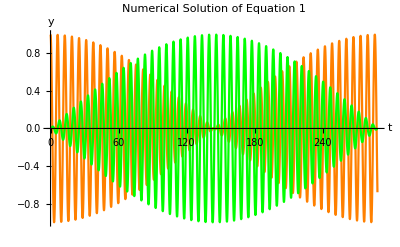

```mathematica
a=1;b=0;c=0;d=0;
{x1solna[t_]} = {x1[t]} /. Flatten[NDSolve[ivp[γ], x1[t], {t, 0, (2 Pi)/γ}]];
{x2solna[t_]} = {x2[t]} /. Flatten[NDSolve[ivp[γ], x2[t], {t, 0, (2 Pi)/γ}]];
graphx1a = Plot[x1solna[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Orange];
graphx2a = Plot[x2solna[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 2",PlotStyle->Green];

Show[graphx1a, graphx2a]
```

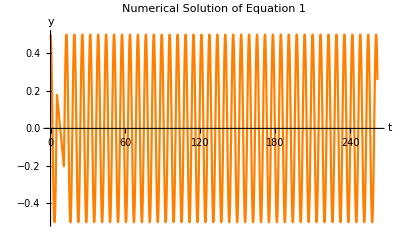

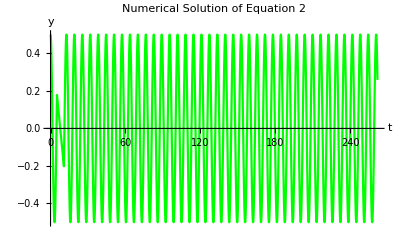

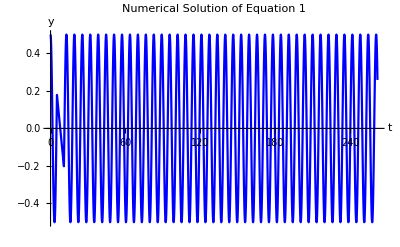

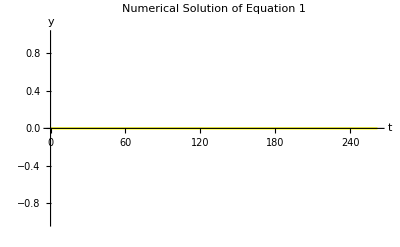

```mathematica
a=1/2;b=0;c=1/2;d=0;
{x1solnb[t_]} = {x1[t]} /. Flatten[NDSolve[ivp[γ], x1[t], {t, 0, (2 Pi)/γ}]];
{x2solnb[t_]} = {x2[t]} /. Flatten[NDSolve[ivp[γ], x2[t], {t, 0, (2 Pi)/γ}]];
graphx1b = Plot[x1solnb[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Orange];
graphx2b = Plot[x2solnb[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 2",PlotStyle->Green];
graphx3b = Plot[(x1solnb[t]+x2solnb[t])/2, {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Blue];
graphx4b = Plot[(x1solnb[t]-x2solnb[t])/2, {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Yellow];

Show[graphx1b]
Show[graphx2b]
Show[graphx3b]
Show[graphx4b]
```

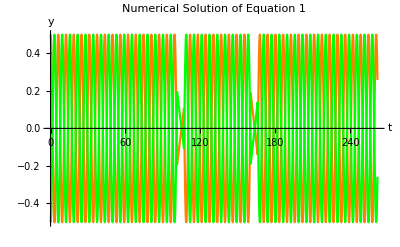

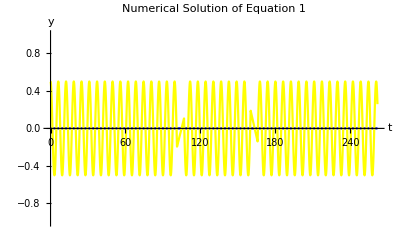

```mathematica
a=1/2;b=0;c=-1/2;d=0;
{x1solnc[t_]} = {x1[t]} /. Flatten[NDSolve[ivp[γ], x1[t], {t, 0, (2 Pi)/γ}]];
{x2solnc[t_]} = {x2[t]} /. Flatten[NDSolve[ivp[γ], x2[t], {t, 0, (2 Pi)/γ}]];
graphx1c = Plot[x1solnc[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Orange];
graphx2c = Plot[x2solnc[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 2",PlotStyle->Green];
graphx3c = Plot[(x1solnc[t]+x2solnc[t])/2, {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Blue];
graphx4c = Plot[(x1solnc[t]-x2solnc[t])/2, {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Yellow];
Show[graphx1c, graphx2c]
Show[graphx3c, graphx4c]
```

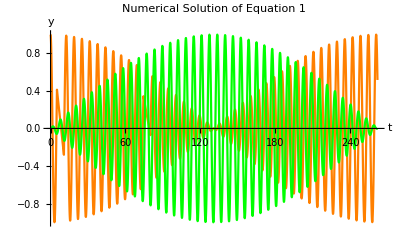

```mathematica
graphx1d = Plot[x1solnb[t]+x1solnc[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1",PlotStyle->Orange];
graphx2d = Plot[x2solnb[t]+x2solnc[t], {t, 0, (2 Pi)/γ}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 2",PlotStyle->Green];
Show[graphx1d, graphx2d]
```